```mathematica
Quit[]
```

## Chapter 1: Setting up xAct

```mathematica
<<xAct`xTensor`;
<<xAct`xTras`;
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external mac executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Commutator::argtu: Commutator called with 1 argument; 2 or 3 arguments are expected.

UpSetDelayed::write: Tag Commutator in ProductQ[Commutator[prod_]] is Protected.

Commutator::argtu: Commutator called with 1 argument; 2 or 3 arguments are expected.

UpSetDelayed::write: Tag Commutator in ScalarsOfProduct[Commutator[prod_]] is Protected.

Commutator::argtu: Commutator called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Commutator::argtu will be suppressed during this calculation.

UpSetDelayed::write: Tag Commutator in ProductByScalar[Commutator[prod_]] is Protected.

General::stop: Further output of UpSetDelayed::write will be suppressed during this calculation.

SetDelayed::write: Tag Commutator in Commutator[prod_][left$___,0,right$___] is Protected.

SetDelayed::write: Tag Commutator in Commutator[prod_][left$___,sum$_Plus,right$___] is Protected.

SetDelayed::write: Tag Commutator in Commutator[prod_][left$___,sum$_SeriesData,right$___] is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Anticommutator::argtu: Anticommutator called with 1 argument; 2 or 3 arguments are expected.

General::stop: Further output of Anticommutator::argtu will be suppressed during this calculation.

------------------------------------------------------------

Package xAct`xPert`  version 1.0.6, {2018,2,28}

CopyRight (C) 2005-2020, David Brizuela, Jose M. Martin-Garcia and Guillermo A. Mena Marugan, under the General Public License.

** Variable $PrePrint assigned value ScreenDollarIndices

** Variable $CovDFormat changed from Prefix to Postfix

** Option AllowUpperDerivatives of ContractMetric changed from False to True

** Option MetricOn of MakeRule changed from None to All

** Option ContractMetrics of MakeRule changed from False to True

------------------------------------------------------------

Package xAct`Invar`  version 2.0.5, {2013,7,1}

CopyRight (C) 2006-2020, J. M. Martin-Garcia, D. Yllanes and R. Portugal, under the General Public License.

** DefConstantSymbol: Defining constant symbol sigma.

** DefConstantSymbol: Defining constant symbol dim.

** Option CurvatureRelations of DefCovD changed from True to False

** Variable $CommuteCovDsOnScalars changed from True to False

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`SymManipulator`  version 0.9.5, {2021,9,14}

CopyRight (C) 2011-2021, Thomas Bäckdahl, under the General Public License.

------------------------------------------------------------

Package xAct`xTras`  version 1.4.2, {2014,10,30}

CopyRight (C) 2012-2014, Teake Nutma, under the General Public License.

** Variable $CovDFormat changed from Postfix to Prefix

** Option CurvatureRelations of DefCovD changed from False to True

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,n]]
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

```mathematica
DefChart[ch,M,{0,1,2,3},{t[],x[],y[],z[]},ChartColor->Purple]
```

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar x[].

** DefTensor: Defining coordinate scalar y[].

** DefTensor: Defining coordinate scalar z[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-b,-c,-d].

```mathematica
DefConstantSymbol[Mp]
DefConstantSymbol[Λ]
```

** DefConstantSymbol: Defining constant symbol Mp.

** DefConstantSymbol: Defining constant symbol Λ.

```mathematica
DefScalarFunction[aa]
DefScalarFunction[nn]
DefScalarFunction[ϕ]
DefScalarFunction[ψ]
DefScalarFunction[ϖ]
```

** DefScalarFunction: Defining scalar function aa.

** DefScalarFunction: Defining scalar function nn.

** DefScalarFunction: Defining scalar function ϕ.

** DefScalarFunction: Defining scalar function ψ.

** DefScalarFunction: Defining scalar function ϖ.

```mathematica
metricmatrix={{nn[t[]]^2,0,0,0},{0,-aa[t[]]^2,0,0},{0,0,-aa[t[]]^2,0},{0,0,0,-aa[t[]]^2}};
```

```mathematica
metricmatrix//MatrixForm
```

(nn[t]^2 | 0 | 0 | 0
0 | -aa[t]^2 | 0 | 0
0 | 0 | -aa[t]^2 | 0
0 | 0 | 0 | -aa[t]^2)

```mathematica
metric=CTensor[metricmatrix,{-ch,-ch}]
```

CTensor[{{nn[t]^2,0,0,0},{0,-aa[t]^2,0,0},{0,0,-aa[t]^2,0},{0,0,0,-aa[t]^2}},{-ch,-ch},0]

```mathematica
SetCMetric[metric,ch,SignatureOfMetric->{1,3,0}]
cd=CovDOfMetric[metric]
```

CCovD[PDch,CTensor[{{{nn'[t]/nn[t],0,0,0},{0,(aa[t] aa'[t])/nn[t]^2,0,0},{0,0,(aa[t] aa'[t])/nn[t]^2,0},{0,0,0,(aa[t] aa'[t])/nn[t]^2}},{{0,aa'[t]/aa[t],0,0},{aa'[t]/aa[t],0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,aa'[t]/aa[t],0},{0,0,0,0},{aa'[t]/aa[t],0,0,0},{0,0,0,0}},{{0,0,0,aa'[t]/aa[t]},{0,0,0,0},{0,0,0,0},{aa'[t]/aa[t],0,0,0}}},{ch,-ch,-ch},0],CTensor[{{nn[t]^2,0,0,0},{0,-aa[t]^2,0,0},{0,0,-aa[t]^2,0},{0,0,0,-aa[t]^2}},{-ch,-ch},0]]

```mathematica
detg = Det[metricmatrix]
```

-aa[t]^6 nn[t]^2

```mathematica
Riemanncd=Riemann[cd];
Riccicd=Ricci[cd];
RicciScalarcd=RicciScalar[cd];
```

```mathematica
RicciScalarcd[]//FullSimplify
```

(6 aa[t] aa'[t] nn'[t]-6 nn[t] (aa'[t]^2+aa[t] aa''[t]))/(aa[t]^2 nn[t]^3)

## Chapter 2: Finding Equations of Motion

## Equations of motion

### Define parameters and Lagrangian:

```mathematica
phi=CTensor[ϕ[t[]],{}];
psi = CTensor[ψ[t[]],{}];
Varpi = CTensor[ϖ[t[]],{}];
```

```mathematica
Xϕ=1/2cd[-a]@phi[]cd[a]@phi[]//ContractBasis//Simplification;
Xψ = 1/2 cd[-a]@psi[] cd[a]@psi[]//ContractBasis //FullSimplify;
```

```mathematica
DefTensor[J[a],M];
```

** DefTensor: Defining tensor J[a].

```mathematica
J[a_] := 4 σ1 psi[]^3 cd[a]@(phi[]/psi[]) -Mp^2 υ2 cd[a]@phi[];
JJ = J[-a] J[a] //ContractBasis//FullSimplify;
```

Note that there is an absolute value in the √JJ term, but in this case we have set it to not do anything

```mathematica
fnothing[x_] := x;
 sqJJ = Assuming[{Mp>0,ζ >0,ψ[t]>0,ϕ[t]>0 ,ψ'[t]>0, ϕ'[t]>0, υ2>0,σ1>0, nn[t]>0},Refine[√JJ]]/. Abs-> fnothing
```

((Mp^2 υ2-4 σ1 ψ[t]^2) ϕ'[t]+4 σ1 ϕ[t] ψ[t] ψ'[t])/nn[t]

Now we look at our Lagrangian:

```mathematica
L=Sqrt[-detg]((1/2 Mp^2 υ2-1/2 σ2 psi[]^2)RicciScalarcd[] - 12(1/2 σ2 Xψ)+sqJJ+3/4 Mp^2(υ2 phi[]^2 +4 υ1 psi[]^2)-3/2 2σ2 phi[]^2 psi[]^2);
```

We modify the Lagrangian by using the following relations:

```mathematica
υ1 =0
```

0

```mathematica
Clear[υ2]
```

```mathematica
σ1 = σ2 ϛ;
ψ[t_] := (Mp √(υ2) ϖ[t])/(√(4 σ1));
```

```mathematica
(*ϕ[t_] :=ϱ[t]*)
```

The new Lagrangian is then:

```mathematica
Lnew=FullSimplify[L/.{t[]->t},Assumptions->{aa[t]>0,nn[t]>0}]
```

(Mp^2 υ2 aa[t] (3 nn[t] (-4 ϛ+ϖ[t]^2) aa'[t]^2+aa[t]^2 nn[t] (3 nn[t]^2 (ϛ-ϖ[t]^2) ϕ[t]^2-3 ϖ'[t]^2+4 ϛ nn[t] (ϖ[t] ϕ[t] ϖ'[t]-(-1+ϖ[t]^2) ϕ'[t]))+3 aa[t] (4 ϛ-ϖ[t]^2) (aa'[t] nn'[t]-nn[t] aa''[t])))/(4 ϛ nn[t]^2)

### Equations of Motion

```mathematica
Eqn=Sum[(-1)^it D[D[Lnew,Derivative[it][nn][t]],{t,it}],{it,0,2}]- ρ[t] aa[t]^3//FullSimplify;
Eqa=Sum[(-1)^it D[D[Lnew,Derivative[it][aa][t]],{t,it}],{it,0,2}]+ 3P[t] aa[t]^2//FullSimplify;
Eqϕ=Sum[(-1)^it D[D[Lnew,Derivative[it][ϕ][t]],{t,it}],{it,0,2}]//FullSimplify;
Eqψ=Sum[(-1)^it D[D[Lnew,Derivative[it][ϖ][t]],{t,it}],{it,0,2}]//FullSimplify;
```

```mathematica
nn[t_]:=1;
```

As one can see from the above equations, ρ[t] and P[t] are added to the Equations of motion as a variation of the energy-momentum tensor.
We want to write the energy density and pressure in terms of the big Omegas:

```mathematica
(*ρm[t_]:= 3 Mp^2 H00^2 Ωm0 aa[t]^-3;
ρr[t_]:= 3 Mp^2 H00^2 Ωr0 aa[t]^-4;*)
(*ρΛ[t_]:=3 Mp^2 H00^2 ΩΛ0;*)
ρ[t_]:=ρm[t]+ρr[t]+ρΛ[t];
P[t_]:=1/3 ρr[t]-ρΛ[t];
```

One more thing we note is that the third equation gives a definition of ϕ which significantly simplifies the rest of the equations

```mathematica
ϕ[t_] =ϕ[t]/.Flatten[DSolve[Eqϕ==0, ϕ[t],t]]
```

-(2 ϛ (-aa'[t]+ϖ[t]^2 aa'[t]+aa[t] ϖ[t] ϖ'[t]))/(aa[t] (ϛ-ϖ[t]^2))

Let’s look at how the other three EOMs are now:

```mathematica
Eqn//FullSimplify
Eqa //FullSimplify
Eqψ //FullSimplify
```

(aa[t] (-4 ϛ aa[t]^2 (ρm[t]+ρr[t]+ρΛ[t])+3 Mp^2 υ2 (-4 ϛ+ϖ[t]^2) aa'[t]^2+6 Mp^2 υ2 aa[t] ϖ[t] aa'[t] ϖ'[t]+3 Mp^2 υ2 aa[t]^2 ϖ'[t]^2+(12 Mp^2 υ2 ϛ^2 ((-1+ϖ[t]^2) aa'[t]+aa[t] ϖ[t] ϖ'[t])^2)/(ϛ-ϖ[t]^2)))/(4 ϛ)

1/(4 ϛ)3 ((Mp^2 υ2 ϖ[t]^2 (ϛ (-5+8 ϛ)+(1-4 ϛ^2) ϖ[t]^2) aa'[t]^2)/(-ϛ+ϖ[t]^2)+(2 Mp^2 υ2 aa[t] ϖ[t] (2 ((5-8 ϛ) ϛ^2+(-1+4 ϛ^2) ϖ[t]^2 (2 ϛ-ϖ[t]^2)) aa'[t] ϖ'[t]-ϖ[t] (-ϛ+ϖ[t]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[t]^2) aa''[t]))/((ϛ-ϖ[t]^2)^2)+1/3 aa[t]^2 (4 ϛ ρr[t]-12 ϛ ρΛ[t]+(3 Mp^2 υ2 ((-ϛ^2 (1+8 ϛ)+2 ϛ (1-4 ϛ+6 ϛ^2) ϖ[t]^2+(-1+4 ϛ^2) ϖ[t]^4) ϖ'[t]^2-2 ϖ[t] (-ϛ+ϖ[t]^2) (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[t]^2) ϖ''[t]))/((ϛ-ϖ[t]^2)^2)))

1/(2 ϛ (ϛ-ϖ[t]^2)^2)3 Mp^2 υ2 aa[t] (-((-1+4 ϛ^2) ϖ[t]^5 (aa'[t]^2+aa[t] aa''[t]))+ϛ^2 ϖ[t] (-3 aa'[t]^2+4 ϛ aa[t]^2 ϖ'[t]^2+(1-4 ϛ) aa[t] aa''[t])+2 ϛ ϖ[t]^3 ((-1+4 ϛ) aa'[t]^2+(-1+2 ϛ (1+ϛ)) aa[t] aa''[t])+ϛ^2 aa[t] (3 aa'[t] ϖ'[t]+aa[t] ϖ''[t])+2 ϛ (-1+2 ϛ^2) aa[t] ϖ[t]^2 (3 aa'[t] ϖ'[t]+aa[t] ϖ''[t])-(-1+4 ϛ^2) aa[t] ϖ[t]^4 (3 aa'[t] ϖ'[t]+aa[t] ϖ''[t]))

## Find varpi at each matter dominated epoch

### This is for normal time:

```mathematica
Clear[H]
```

```mathematica
F1const = Eqn/.ϖ'[t]->0/.(aa'[t]-> H[t]aa[t])/.ϖ[t]->ϖ/.H[t]-> √H2//FullSimplify
```

(aa[t]^3 ((3 H2 Mp^2 ϖ^2 υ2 (ϖ^2-5 ϛ-4 (-2+ϖ^2) ϛ^2))/(ϖ^2-ϛ)-4 ϛ (ρm[t]+ρr[t]+ρΛ[t])))/(4 ϛ)

```mathematica
F1GR = FullSimplify[F1const/.ϖ->1]/.ϛ->1/.υ2->-4/3
```

-1/4 aa[t]^3 (-12 H2 Mp^2+4 (ρm[t]+ρr[t]+ρΛ[t]))

```mathematica
F1H2 = H2/.Flatten[Solve[F1const==0, H2]]/.Mp-> 1/√κ
```

-(4 κ (ϖ^2-ϛ) ϛ (ρm[t]+ρr[t]+ρΛ[t]))/(3 ϖ^2 υ2 (-ϖ^2+5 ϛ-8 ϛ^2+4 ϖ^2 ϛ^2))

```mathematica
F1GRH2 = H2/.Flatten[Solve[F1GR  ==0, H2]]/.Mp-> 1/√(gi κ)
```

1/3 gi κ (ρm[t]+ρr[t]+ρΛ[t])

```mathematica
givalue = gi /. Flatten[Solve[F1H2 == F1GRH2, gi]]
```

-(4 (ϖ^2-ϛ) ϛ)/(ϖ^2 υ2 (-ϖ^2+5 ϛ-8 ϛ^2+4 ϖ^2 ϛ^2))

```mathematica
(*modified friedmann equation with gneuton baked in*)
(*Numerically extract ϖ: Friedmann equation from GR but with g_n, replaced by this formula, compare with our fully solved equations*)
(*Interpolate between epochs and then test numerically determined wi*)
```

### try

```mathematica
Eqn/.aa'[t]^2-> H2 aa[t]^2//FullSimplify
```

(aa[t]^2 (3 H2 Mp^2 υ2 aa[t] (-4 ϛ+ϖ[t]^2)+6 Mp^2 υ2 ϖ[t] aa'[t] ϖ'[t]+aa[t] (-4 ϛ (ρm[t]+ρr[t]+ρΛ[t])+3 Mp^2 υ2 ϖ'[t]^2+(12 Mp^2 υ2 ϛ^2 ((-1+ϖ[t]^2) aa'[t]+aa[t] ϖ[t] ϖ'[t])^2)/(aa[t]^2 (ϛ-ϖ[t]^2)))))/(4 ϛ)

```mathematica
Solve[{Eqn/.aa'[t]^2-> H2 aa[t]^2} ==0, H2]//FullSimplify
```

{{H2→-(-(4 ϛ (ρm[t]+ρr[t]+ρΛ[t]))/(Mp^2 υ2)+(6 ϖ[t] aa'[t] ϖ'[t])/aa[t]+3 ϖ'[t]^2+(12 (ϛ (-1+ϖ[t]^2) aa'[t]+ϛ aa[t] ϖ[t] ϖ'[t])^2)/(aa[t]^2 (ϛ-ϖ[t]^2)))/(3 (-4 ϛ+ϖ[t]^2))}}

```mathematica
F12H2 = H2/.Flatten[Solve[{Eqn/.aa'[t]^2-> H2 aa[t]^2} ==0, H2]]/.Mp-> 1/√κ//FullSimplify
```

-(-(4 κ ϛ (ρm[t]+ρr[t]+ρΛ[t]))/υ2+(6 ϖ[t] aa'[t] ϖ'[t])/aa[t]+3 ϖ'[t]^2+(12 (ϛ (-1+ϖ[t]^2) aa'[t]+ϛ aa[t] ϖ[t] ϖ'[t])^2)/(aa[t]^2 (ϛ-ϖ[t]^2)))/(3 (-4 ϛ+ϖ[t]^2))

```mathematica
Solve[F12H2 == F1GRH2, gi]//FullSimplify
```

{{gi→-(-(4 κ ϛ (ρm[t]+ρr[t]+ρΛ[t]))/υ2+(6 ϖ[t] aa'[t] ϖ'[t])/aa[t]+3 ϖ'[t]^2+(12 (ϛ (-1+ϖ[t]^2) aa'[t]+ϛ aa[t] ϖ[t] ϖ'[t])^2)/(aa[t]^2 (ϛ-ϖ[t]^2)))/(κ (-4 ϛ+ϖ[t]^2) (ρm[t]+ρr[t]+ρΛ[t]))}}

```mathematica
F12H2 = H2/.Flatten[Solve[{Eqn/.aa'[t]-> √H2 aa[t]} ==0, H2]]/.Mp-> 1/√κ//FullSimplify
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

1/(3 υ2^2 ϖ[t]^4 (ϛ (-5+8 ϛ)+(1-4 ϛ^2) ϖ[t]^2)^2)(4 κ υ2 ϛ ϖ[t]^2 (ϛ-ϖ[t]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[t]^2) (ρm[t]+ρr[t]+ρΛ[t])+3 υ2^2 ϖ[t]^2 (ϛ^2 (-3+8 ϛ (-1+4 ϛ))-2 ϛ (-1+2 ϛ) (1+2 ϛ) (1+4 ϛ) ϖ[t]^2+(1-4 ϛ^2)^2 ϖ[t]^4) ϖ'[t]^2-4 √3 κ^2 √((υ2^3 ϛ ϖ[t]^4 (ϛ-ϖ[t]^2) (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[t]^2)^2 ϖ'[t]^2 (κ ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[t]^2) (ρm[t]+ρr[t]+ρΛ[t])+3 υ2 (-1+4 ϛ^2) ϖ'[t]^2))/κ^4))

```mathematica
Solve[F12H2 == F1GRH2, gi]//FullSimplify
```

{{gi→(4 κ υ2 ϛ ϖ[t]^2 (ϛ-ϖ[t]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[t]^2) (ρm[t]+ρr[t]+ρΛ[t])+3 υ2^2 ϖ[t]^2 (ϛ^2 (-3+8 ϛ (-1+4 ϛ))-2 ϛ (-1+2 ϛ) (1+2 ϛ) (1+4 ϛ) ϖ[t]^2+(1-4 ϛ^2)^2 ϖ[t]^4) ϖ'[t]^2-4 √3 κ^2 √((υ2^3 ϛ ϖ[t]^4 (ϛ-ϖ[t]^2) (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[t]^2)^2 ϖ'[t]^2 (κ ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[t]^2) (ρm[t]+ρr[t]+ρΛ[t])+3 υ2 (-1+4 ϛ^2) ϖ'[t]^2))/κ^4))/(κ υ2^2 ϖ[t]^4 (ϛ (-5+8 ϛ)+(1-4 ϛ^2) ϖ[t]^2)^2 (ρm[t]+ρr[t]+ρΛ[t]))}}

### Getting relations

```mathematica
Hi = 2/(3(1+ wi)t)
```

2/(3 t (1+wi))

```mathematica
HH[t_]:= aa'[t]/aa[t]
```

```mathematica
Solve[HH'[t]==D[Hi, t], aa''[t]]
```

{{aa''[t]→aa[t] (-2/(3 t^2 (1+wi))+aa'[t]^2/aa[t]^2)}}

```mathematica
Eqsolve = Eqψ /.ϖ'[t]->0/.ϖ''[t]->0/.ϖ[t]->ϖ/.Flatten[Solve[-aa'[t]^2/aa[t]^2+aa''[t]/aa[t]==D[Hi, t], aa''[t]]]/.aa'[t] -> Hi aa[t]/.ϖ -> √ϖ2//FullSimplify
```

(Mp^2 √ϖ2 υ2 ((-1+3 wi) ϖ2^2 (-1+4 ϛ^2)+ϛ^2 (-7+4 ϛ+3 wi (-1+4 ϛ))-2 ϖ2 ϛ (1+2 (-3+ϛ) ϛ+wi (-3+6 ϛ (1+ϛ)))) aa[t]^3)/(3 t^2 (1+wi)^2 (ϖ2-ϛ)^2 ϛ)

```mathematica
Solve[Eqsolve ==0, ϖ2]//FullSimplify
```

{{ϖ2→0},{ϖ2→(-2 √((-1+ϛ)^2 ϛ^2 (2-6 wi+(ϛ+3 wi ϛ)^2))+ϛ (1+2 (-3+ϛ) ϛ+wi (-3+6 ϛ (1+ϛ))))/((-1+3 wi) (-1+4 ϛ^2))},{ϖ2→(2 √((-1+ϛ)^2 ϛ^2 (2-6 wi+(ϛ+3 wi ϛ)^2))+ϛ (1+2 (-3+ϛ) ϛ+wi (-3+6 ϛ (1+ϛ))))/((-1+3 wi) (-1+4 ϛ^2))}}

```mathematica
gisolution = givalue/.ϖ->√ϖ2/.Solve[Eqsolve ==0, ϖ2]//FullSimplify
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,(4 ((3-9 wi) ϛ-(1+3 wi)^2 ϛ^3+(ϛ+3 wi ϛ)^2-(1+3 wi) √((-1+ϛ)^2 ϛ^2 (2-6 wi+(ϛ+3 wi ϛ)^2))))/(υ2 ϛ (1+6 wi (-1+ϛ)+2 ϛ) (-7+4 ϛ+3 wi (-1+4 ϛ))),(4 ((3-9 wi) ϛ-(1+3 wi)^2 ϛ^3+(ϛ+3 wi ϛ)^2+(1+3 wi) √((-1+ϛ)^2 ϛ^2 (2-6 wi+(ϛ+3 wi ϛ)^2))))/(υ2 ϛ (1+6 wi (-1+ϛ)+2 ϛ) (-7+4 ϛ+3 wi (-1+4 ϛ)))}

```mathematica
giup2minus[wi_,ϛ_] := gisolution[[2]]υ2//FullSimplify
```

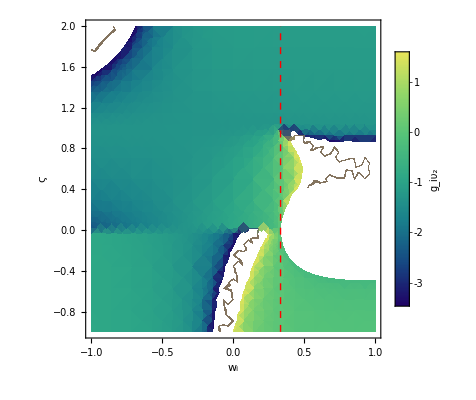

```mathematica
DensityPlot[giup2minus[wi,ϛ],{wi,-1,1},{ϛ,-1,2},FrameLabel->{"w_i","ϛ"}, ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[Automatic,LegendLabel->"g_iυ_2"],Epilog->{Red,Dashed,Line[{{1/3,-1},{1/3,2}}]}]
```

```mathematica
giup2plus[wi_,ϛ_] := gisolution[[3]]υ2//FullSimplify
```

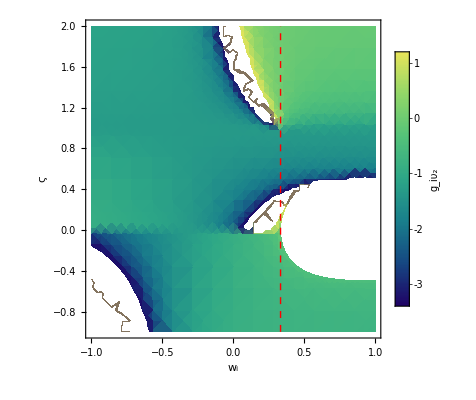

```mathematica
DensityPlot[giup2plus[wi,ϛ] ,{wi,-1,1},{ϛ,-1,2},FrameLabel->{"w_i","ϛ"}, ColorFunction->"BlueGreenYellow",PlotLegends->BarLegend[Automatic,LegendLabel->"g_iυ_2"],Epilog->{Red,Dashed,Line[{{1/3,-1},{1/3,2}}]}]
```

## Get Equations

```mathematica
rule = {ϖ:>(ϖ[τ[#]] &),aa:>( α aa[τ[#]] &)}
rule2 = {ρm:>(ρm[τ[#]] &), ρr:>(ρr[τ[#]] &), ρΛ:>(ρΛ[τ[#]] &), pm:>(pm[τ[#]] &),pr:>(pr[τ[#]] &), pΛ:>(pΛ[τ[#]] &)}
```

{ϖ:>(ϖ[τ[#1]]&),aa:>(α aa[τ[#1]]&)}

{ρm:>(ρm[τ[#1]]&),ρr:>(ρr[τ[#1]]&),ρΛ:>(ρΛ[τ[#1]]&),pm:>(pm[τ[#1]]&),pr:>(pr[τ[#1]]&),pΛ:>(pΛ[τ[#1]]&)}

```mathematica
E1=Eqψ /.rule /.rule2/.τ''[t]-> D[1/(α aa[τ[t]]),t]/.τ'[t]-> 1/(α aa[τ])/.τ[t]-> τ//FullSimplify
F1 = Eqn /.rule /.rule2/.τ''[t]-> D[1/(α aa[τ[t]]),t]/.τ'[t]-> 1/(α aa[τ])/.τ[t]-> τ//FullSimplify
F2 = Eqa/.rule  /.rule2/.τ''[t]-> D[1/(α aa[τ[t]]),t]/.τ'[t]-> 1/(α aa[τ])/.τ[t]-> τ//FullSimplify
```

1/(2 ϛ aa[τ] (ϛ-ϖ[τ]^2)^2)3 Mp^2 α υ2 ((1-4 ϛ^2) aa[τ] ϖ[τ]^5 aa''[τ]+ϛ^2 ϖ[τ] (4 (-1+ϛ) aa'[τ]^2+4 ϛ aa[τ]^2 ϖ'[τ]^2+(1-4 ϛ) aa[τ] aa''[τ])+2 ϛ ϖ[τ]^3 (-2 (-1+ϛ) ϛ aa'[τ]^2+(-1+2 ϛ (1+ϛ)) aa[τ] aa''[τ])+ϛ^2 aa[τ] (2 aa'[τ] ϖ'[τ]+aa[τ] ϖ''[τ])+2 ϛ (-1+2 ϛ^2) aa[τ] ϖ[τ]^2 (2 aa'[τ] ϖ'[τ]+aa[τ] ϖ''[τ])-(-1+4 ϛ^2) aa[τ] ϖ[τ]^4 (2 aa'[τ] ϖ'[τ]+aa[τ] ϖ''[τ]))

(α (-4 α^2 ϛ aa[τ]^4 (ρm[τ]+ρr[τ]+ρΛ[τ])+3 Mp^2 υ2 (-4 ϛ+ϖ[τ]^2) aa'[τ]^2+6 Mp^2 υ2 aa[τ] ϖ[τ] aa'[τ] ϖ'[τ]+3 Mp^2 υ2 aa[τ]^2 ϖ'[τ]^2+(12 Mp^2 υ2 ϛ^2 ((-1+ϖ[τ]^2) aa'[τ]+aa[τ] ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ aa[τ])

1/(4 ϛ aa[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 α^2 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ρr[τ]-3 ρΛ[τ])+3 Mp^2 υ2 ϖ[τ]^2 (-ϛ+ϖ[τ]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) aa'[τ]^2+6 Mp^2 υ2 aa[τ] ϖ[τ] ((3 (3-4 ϛ) ϛ^2+2 ϛ (-1-2 ϛ+6 ϛ^2) ϖ[τ]^2+(1-4 ϛ^2) ϖ[τ]^4) aa'[τ] ϖ'[τ]-ϖ[τ] (-ϛ+ϖ[τ]^2) ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) aa''[τ])+3 Mp^2 υ2 aa[τ]^2 ((-ϛ^2 (1+8 ϛ)+2 ϛ (1-4 ϛ+6 ϛ^2) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) ϖ'[τ]^2-2 ϖ[τ] (-ϛ+ϖ[τ]^2) (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) ϖ''[τ]))

```mathematica
rhoGRrules = {ρm[τ]:> ρmGR[τ], ρr[τ]:> ρrGR[τ], ρΛ[τ]:> ρΛGR[τ],pm[τ]:> pmGR[τ], pr[τ]:> prGR[τ], pΛ[τ]:> pΛGR[τ]}
```

{ρm[τ]:>ρmGR[τ],ρr[τ]:>ρrGR[τ],ρΛ[τ]:>ρΛGR[τ],pm[τ]:>pmGR[τ],pr[τ]:>prGR[τ],pΛ[τ]:>pΛGR[τ]}

Getting Equations for GR:

```mathematica
F1/.ϖ'[τ]->0//FullSimplify
```

-α^3 aa[τ]^3 (ρm[τ]+ρr[τ]+ρΛ[τ])+(3 Mp^2 α υ2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) aa'[τ]^2)/(4 ϛ aa[τ] (ϛ-ϖ[τ]^2))

```mathematica
F1GRtau = F1/.ϖ'[τ]->0/. ϖ[τ]->1/.aa'[τ]->ℋ/α/.λ->ρΛGR[τ]/(3 H00^2 Mp^2)/.ϛ->1/.υ2->-4/3/.ℋ^2->ℋ2/.α->1/.rhoGRrules//FullSimplify
```

(3 Mp^2 ℋ2)/aa[τ]-aa[τ]^3 (ρmGR[τ]+ρrGR[τ]+ρΛGR[τ])

```mathematica
F1GRH = ℋ2/. Flatten[Solve[F1GRtau==0, ℋ2]]/.ρΛGR[τ] -> ρΛeff[τ]//FullSimplify
```

(aa[τ]^4 (ρmGR[τ]+ρrGR[τ]+ρΛeff[τ]))/(3 Mp^2)

Compare to the F1 Equation to find rho:

```mathematica
rhorules = {ρm[τ]-> 3 Mp^2 H00^2 Ωm0 (α aa[τ])^-3,ρr[τ]-> 3 Mp^2 H00^2 Ωr0 (α aa[τ])^-4,ρΛ[τ]->3 Mp^2 H00^2 ΩΛ0}
prulesGR = {pmGR[τ]-> 0, prGR[τ]-> -1/3ρrGR[τ], pΛGR[τ]-> -ρΛGR[τ]}
rhorulesGR =  {ρmGR[τ]-> 3 Mp^2 H00^2 Ωm0 ( aa[τ])^-3,ρrGR[τ]-> 3 Mp^2 H00^2 Ωr0 ( aa[τ])^-4,ρΛGR[τ]->3 Mp^2 H00^2 ΩΛ0}
prules = {pm[τ]->0,pr[τ]-> 1/3 ρr[τ],pΛ[τ]-> - ρΛ[τ]}
```

{ρm[τ]→(3 H00^2 Mp^2 Ωm0)/(α^3 aa[τ]^3),ρr[τ]→(3 H00^2 Mp^2 Ωr0)/(α^4 aa[τ]^4),ρΛ[τ]→3 H00^2 Mp^2 ΩΛ0}

{pmGR[τ]→0,prGR[τ]→-ρrGR[τ]/3,pΛGR[τ]→-ρΛGR[τ]}

{ρmGR[τ]→(3 H00^2 Mp^2 Ωm0)/aa[τ]^3,ρrGR[τ]→(3 H00^2 Mp^2 Ωr0)/aa[τ]^4,ρΛGR[τ]→3 H00^2 Mp^2 ΩΛ0}

{pm[τ]→0,pr[τ]→ρr[τ]/3,pΛ[τ]→-ρΛ[τ]}

```mathematica
F1tau = F1/.aa'[τ]^2->ℋ2/α^2
```

(α ((3 Mp^2 ℋ2 υ2 (-4 ϛ+ϖ[τ]^2))/α^2-4 α^2 ϛ aa[τ]^4 (ρm[τ]+ρr[τ]+ρΛ[τ])+6 Mp^2 υ2 aa[τ] ϖ[τ] aa'[τ] ϖ'[τ]+3 Mp^2 υ2 aa[τ]^2 ϖ'[τ]^2+(12 Mp^2 υ2 ϛ^2 ((-1+ϖ[τ]^2) aa'[τ]+aa[τ] ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ aa[τ])

```mathematica
F1Htau = ℋ2/. Flatten[Solve[F1tau==0, ℋ2]]//FullSimplify
```

(4 α ϛ aa[τ] (α^3 aa[τ]^3 (ρm[τ]+ρr[τ]+ρΛ[τ])-(3 Mp^2 α υ2 ϖ[τ] aa'[τ] ϖ'[τ])/(2 ϛ)-(3 Mp^2 α υ2 aa[τ] ϖ'[τ]^2)/(4 ϛ)-(3 α υ2 ϛ (Mp (-1+ϖ[τ]^2) aa'[τ]+Mp aa[τ] ϖ[τ] ϖ'[τ])^2)/(aa[τ] (ϛ-ϖ[τ]^2))))/(3 Mp^2 υ2 (-4 ϛ+ϖ[τ]^2))

```mathematica
ρe = ρΛeff[τ]/. Flatten[Solve[F1GRH == F1Htau, ρΛeff[τ]]]/.rhorules /.rhorulesGR//FullSimplify//FullSimplify
```

(3 Mp^2 (-H00^2 Ωr0-H00^2 Ωm0 aa[τ]+(4 ϛ (-H00^2 (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4) (ϛ-ϖ[τ]^2)+α^2 υ2 ϛ (-1+ϖ[τ]^2)^2 aa'[τ]^2)+2 α^2 υ2 aa[τ] ϖ[τ] (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) aa'[τ] ϖ'[τ]+α^2 υ2 aa[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2)/(υ2 (4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4))))/aa[τ]^4

To find P:

```mathematica
secdiv =  Flatten[Solve[F2 ==0&& E1 ==0, {aa''[τ],ϖ''[τ]}]]//FullSimplify
```

{aa''[τ]→1/(24 Mp^2 υ2 ϛ (-1+4 ϛ^2) aa[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 α^2 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) (ρr[τ]-3 ρΛ[τ])+3 Mp^2 υ2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) aa'[τ]^2+6 Mp^2 υ2 aa[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ] ϖ'[τ]+3 Mp^2 υ2 aa[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2),ϖ''[τ]→-1/(24 Mp^2 υ2 ϛ (-1+4 ϛ^2) aa[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(4 α^2 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) (ρr[τ]-3 ρΛ[τ])+3 Mp^2 υ2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ]^2+6 Mp^2 υ2 aa[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) aa'[τ] ϖ'[τ]+3 Mp^2 υ2 aa[τ]^2 (ϛ^3 (-1+4 ϛ) (1+8 ϛ)+ϛ^2 (3-8 (ϛ+2 ϛ^3)) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)}

```mathematica
Pefftau = Peff/.Flatten[Solve[D[ρe, τ] == -3 aa'[τ]/aa[τ](ρe+Peff), Peff]]/.secdiv/.prules/.rhorules//FullSimplify
```

-((Mp^2 (α^2 υ2 ϖ[τ]^2 (-4 ϛ+ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ]^3+2 α^2 υ2 aa[τ] ϖ[τ] (16 (7-4 ϛ) ϛ^5-8 ϛ^4 (17+4 ϛ (3+8 (-2+ϛ) ϛ)) ϖ[τ]^2+ϛ^3 (-21+4 ϛ (71+4 ϛ (-3+16 (-3+ϛ) ϛ))) ϖ[τ]^4+ϛ^2 (59+8 ϛ (-17+2 ϛ (-17+ϛ (31+12 ϛ)))) ϖ[τ]^6-ϛ (-1+2 ϛ) (1+2 ϛ) (-15+4 ϛ (3+11 ϛ)) ϖ[τ]^8+(1-4 ϛ^2)^2 ϖ[τ]^10) aa'[τ]^2 ϖ'[τ]+8 ϛ (-1+4 ϛ^2) aa[τ] ϖ[τ]^3 (ϛ-ϖ[τ]^2) ϖ'[τ] (-4 H00^2 ϛ (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4) (ϛ-ϖ[τ]^2)+α^2 υ2 aa[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2)+aa'[τ] (-12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) (4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4)^2+4 H00^2 Ωr0 ϛ (ϛ+(1+υ2) (-1+4 ϛ^2) ϖ[τ]^2) (4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4)^2+α^2 υ2 aa[τ]^2 (-16 ϛ^5 (1+8 ϛ)+8 ϛ^4 (7+8 ϛ) ϖ[τ]^2+ϛ^3 (-89+8 ϛ (23+8 ϛ (3+4 (-3+ϛ) ϛ))) ϖ[τ]^4+ϛ^2 (75+128 ϛ (-1+ϛ (-3+ϛ (4+3 ϛ)))) ϖ[τ]^6-(1-2 ϛ)^2 ϛ (1+2 ϛ) (27+46 ϛ) ϖ[τ]^8+(1-4 ϛ^2)^2 ϖ[τ]^10) ϖ'[τ]^2)))/(4 υ2 ϛ (-1+4 ϛ^2) aa[τ]^4 (4 ϛ^2 ϖ[τ]-5 ϛ ϖ[τ]^3+ϖ[τ]^5)^2 aa'[τ]))

```mathematica
Pe = Pefftau/.aa'[τ]^2-> ℋ2/α^2/.ℋ2->F1Htau/.prules/.rhorules//FullSimplify
```

-((Mp^2 (α^2 υ2 ϖ[τ]^2 (-4 ϛ+ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ]^3+8 ϛ (-1+4 ϛ^2) aa[τ] ϖ[τ]^3 (ϛ-ϖ[τ]^2) ϖ'[τ] (-4 H00^2 ϛ (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4) (ϛ-ϖ[τ]^2)+α^2 υ2 aa[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2)+1/(4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4)2 aa[τ] ϖ[τ] (16 (7-4 ϛ) ϛ^5-8 ϛ^4 (17+4 ϛ (3+8 (-2+ϛ) ϛ)) ϖ[τ]^2+ϛ^3 (-21+4 ϛ (71+4 ϛ (-3+16 (-3+ϛ) ϛ))) ϖ[τ]^4+ϛ^2 (59+8 ϛ (-17+2 ϛ (-17+ϛ (31+12 ϛ)))) ϖ[τ]^6-ϛ (-1+2 ϛ) (1+2 ϛ) (-15+4 ϛ (3+11 ϛ)) ϖ[τ]^8+(1-4 ϛ^2)^2 ϖ[τ]^10) ϖ'[τ] (4 ϛ (-H00^2 (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4) (ϛ-ϖ[τ]^2)+α^2 υ2 ϛ (-1+ϖ[τ]^2)^2 aa'[τ]^2)+2 α^2 υ2 aa[τ] ϖ[τ] (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2) aa'[τ] ϖ'[τ]+α^2 υ2 aa[τ]^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ϖ'[τ]^2)+aa'[τ] (-12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) (4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4)^2+4 H00^2 Ωr0 ϛ (ϛ+(1+υ2) (-1+4 ϛ^2) ϖ[τ]^2) (4 ϛ^2-5 ϛ ϖ[τ]^2+ϖ[τ]^4)^2+α^2 υ2 aa[τ]^2 (-16 ϛ^5 (1+8 ϛ)+8 ϛ^4 (7+8 ϛ) ϖ[τ]^2+ϛ^3 (-89+8 ϛ (23+8 ϛ (3+4 (-3+ϛ) ϛ))) ϖ[τ]^4+ϛ^2 (75+128 ϛ (-1+ϛ (-3+ϛ (4+3 ϛ)))) ϖ[τ]^6-(1-2 ϛ)^2 ϛ (1+2 ϛ) (27+46 ϛ) ϖ[τ]^8+(1-4 ϛ^2)^2 ϖ[τ]^10) ϖ'[τ]^2)))/(4 υ2 ϛ (-1+4 ϛ^2) aa[τ]^4 (4 ϛ^2 ϖ[τ]-5 ϛ ϖ[τ]^3+ϖ[τ]^5)^2 aa'[τ]))

Getting them in Python input form:

```mathematica
rulepython = {ϖ[τ]:> cp,  ϖ'[τ]:> dcp, aa'[τ]:> da,aa[τ]:> a, Ωm :> omega_m, Ωm0 :> omega_m, Ωr0:> Omr, ΩΛ0 :> OmL, α :> a0, H00 :> h*100, Mp^2-> MP2,λ:> lam , ϛ:> stigma, υ2:> v2}
```

{ϖ[τ]:>cp,ϖ'[τ]:>dcp,aa'[τ]:>da,aa[τ]:>a,Ωm:>omega_m,Ωm0:>omega_m,Ωr0:>Omr,ΩΛ0:>OmL,α:>a0,H00:>h 100,Mp^2→MP2,λ:>lam,ϛ:>stigma,υ2:>v2}

```mathematica
ρe /.rulepython//InputForm
```

(3*MP2*(-10000*h^2*Omr - 10000*a*h^2*(omega_m) + (a^2*a0^2*dcp^2*(stigma + cp^2*(-1 + 4*stigma^2))*v2 + 
     2*a*a0^2*cp*da*dcp*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2))*v2 + 
     4*stigma*(a0^2*(-1 + cp^2)^2*da^2*stigma*v2 - 10000*h^2*(-cp^2 + stigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m))))/
    ((cp^4 - 5*cp^2*stigma + 4*stigma^2)*v2)))/a^4

```mathematica
Pe /.rulepython//InputForm
```

-1/4*(MP2*(a0^2*cp^2*da^3*(cp^2 - 4*stigma)^2*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2))*
     ((7 - 4*stigma)*stigma^2 + 2*cp^2*stigma*(1 + 2*(-3 + stigma)*stigma) + cp^4*(-1 + 4*stigma^2))*v2 + 
    da*(-120000*a^4*a0^4*h^2*OmL*stigma*(cp^4 - 5*cp^2*stigma + 4*stigma^2)^2*(stigma + cp^2*(-1 + 4*stigma^2)) + 
      a^2*a0^2*dcp^2*(-16*stigma^5*(1 + 8*stigma) + 8*cp^2*stigma^4*(7 + 8*stigma) - cp^8*(1 - 2*stigma)^2*stigma*(1 + 2*stigma)*(27 + 46*stigma) + 
        cp^10*(1 - 4*stigma^2)^2 + cp^4*stigma^3*(-89 + 8*stigma*(23 + 8*stigma*(3 + 4*(-3 + stigma)*stigma))) + 
        cp^6*stigma^2*(75 + 128*stigma*(-1 + stigma*(-3 + stigma*(4 + 3*stigma)))))*v2 + 40000*h^2*Omr*stigma*(cp^4 - 5*cp^2*stigma + 4*stigma^2)^2*
       (stigma + cp^2*(-1 + 4*stigma^2)*(1 + v2))) + 8*a*cp^3*dcp*stigma*(-cp^2 + stigma)*(-1 + 4*stigma^2)*
     (a^2*a0^2*dcp^2*(stigma + cp^2*(-1 + 4*stigma^2))*v2 - 40000*h^2*stigma*(-cp^2 + stigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m))) + 
    (2*a*cp*dcp*(16*(7 - 4*stigma)*stigma^5 + cp^10*(1 - 4*stigma^2)^2 - cp^8*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(-15 + 4*stigma*(3 + 11*stigma)) - 
       8*cp^2*stigma^4*(17 + 4*stigma*(3 + 8*(-2 + stigma)*stigma)) + cp^4*stigma^3*(-21 + 4*stigma*(71 + 4*stigma*(-3 + 16*(-3 + stigma)*stigma))) + 
       cp^6*stigma^2*(59 + 8*stigma*(-17 + 2*stigma*(-17 + stigma*(31 + 12*stigma)))))*(a^2*a0^2*dcp^2*(stigma + cp^2*(-1 + 4*stigma^2))*v2 + 
       2*a*a0^2*cp*da*dcp*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2))*v2 + 4*stigma*(a0^2*(-1 + cp^2)^2*da^2*stigma*v2 - 
         10000*h^2*(-cp^2 + stigma)*(a^4*a0^4*OmL + Omr + a*a0*(omega_m)))))/(cp^4 - 5*cp^2*stigma + 4*stigma^2)))/
  (a^4*da*stigma*(-1 + 4*stigma^2)*(cp^5 - 5*cp^3*stigma + 4*cp*stigma^2)^2*v2)

## Power series

```mathematica
F1a = F1/.rhorules//FullSimplify;
F2a = F2/.rhorules //FullSimplify;
E1a = E1 /.rhorules //FullSimplify;
```

```mathematica
dcp= ϖ''[τ]/.Flatten[Solve[{F2a==0, E1a==0},{aa''[τ],ϖ''[τ]}]]//FullSimplify
```

1/(8 α^2 υ2 ϛ (-1+4 ϛ^2) aa[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 H00^2 Ωr0 ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ]^2-2 α^2 υ2 aa[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) aa'[τ] ϖ'[τ]+α^2 υ2 aa[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)

```mathematica
Equation1 = F1a
```

(3 Mp^2 α (-(4 H00^2 ϛ (Ωr0+α Ωm0 aa[τ]+α^4 ΩΛ0 aa[τ]^4))/α^2+υ2 (-4 ϛ+ϖ[τ]^2) aa'[τ]^2+2 υ2 aa[τ] ϖ[τ] aa'[τ] ϖ'[τ]+υ2 aa[τ]^2 ϖ'[τ]^2+(4 υ2 (ϛ (-1+ϖ[τ]^2) aa'[τ]+ϛ aa[τ] ϖ[τ] ϖ'[τ])^2)/(ϛ-ϖ[τ]^2)))/(4 ϛ aa[τ])

```mathematica
Equation2 = ϖ''[τ]-dcp
```

-1/(8 α^2 υ2 ϛ (-1+4 ϛ^2) aa[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 H00^2 Ωr0 ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4) aa'[τ]^2-2 α^2 υ2 aa[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6) aa'[τ] ϖ'[τ]+α^2 υ2 aa[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6) ϖ'[τ]^2)+ϖ''[τ]

```mathematica
aSeries[τ_,order_]:=Sum[na[i] τ^i,{i,1,order}]
ϖSeries[τ_,order_]:=ϖr+Sum[nϖ[i] τ^i,{i,1,order}]
```

```mathematica
assumptions={_∈Reals,α>0,υ2<0,H00>0,Ωr0>0,ΩΛ0>0,Ωm0 >0,nϖ[0]>0, ϖr>0,ϛ>0};
$Assumptions=assumptions;
```

```mathematica
expandedEq1=Series[
  Equation1/. {aa->Function[{τ},aSeries[τ,3]],ϖ->Function[{τ},ϖSeries[τ,2]]},
  {τ,0,3}
];
```

```mathematica
expandedEq2=Series[
  Equation2/. {aa->Function[{τ},aSeries[τ,3]],ϖ->Function[{τ},ϖSeries[τ,2]]},
  {τ,0,3}
];
```

```mathematica
order1Eqs={
  Coefficient[expandedEq1,τ,-1],
  Coefficient[expandedEq2,τ,-2]
};

order2Eqs={
  Coefficient[expandedEq1,τ,0],
  Coefficient[expandedEq2,τ,-1]
};
```

```mathematica
order3Eqs={
  Coefficient[expandedEq1,τ,1],
  Coefficient[expandedEq2,τ,0]
};
```

```mathematica
order1Eqs[[1]]
```

(3 Mp^2 α (-(4 H00^2 Ωr0 ϛ)/α^2+υ2 (ϖr^2-4 ϛ) na[1]^2+(4 (-1+ϖr^2)^2 υ2 ϛ^2 na[1]^2)/(-ϖr^2+ϛ)))/(4 ϛ na[1])

```mathematica
order1Eqs[[1]]
```

(3 Mp^2 α (-(4 H00^2 Ωr0 ϛ)/α^2+υ2 (ϖr^2-4 ϛ) na[1]^2+(4 (-1+ϖr^2)^2 υ2 ϛ^2 na[1]^2)/(-ϖr^2+ϛ)))/(4 ϛ na[1])

```mathematica
sol1 = Solve[order1Eqs[[1]]==0, na[1],Assumptions->{_∈Reals,α>0,υ2<0,H00>0,Ωr0>0,ΩΛ0>0,Ωm0 >0,nϖ[0]>0, ϖr>0,ϛ>0}]//FullSimplify
```

{{na[1]→-(2 ⅈ H00 √(Ωr0 (ϖr^2-ϛ) ϛ))/(α ϖr √(υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2))))},{na[1]→(2 ⅈ H00 √(Ωr0 (ϖr^2-ϛ) ϛ))/(α ϖr √(υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2))))}}

```mathematica
PowerExpand
```

```mathematica
(*PowerExpand*)
(*Claude with .m file -- nb to .m, when you see this expression in .m file, write that in latex in verbaten, don't try to do math, InputForm then feed to claude, prompt claude to write a dictionary of variables in workflow and latex variables in it, don't let claude do it itself, let claude build a tool*)
```

```mathematica
test = {ϛ->1, υ2->-4/3, ΩΛ0->ΩL}
```

{ϛ→1,υ2→-4/3,ΩΛ0→ΩL}

```mathematica
sol1 /.test//FullSimplify
```

{{na[1]→-(H00 √Ωr0)/(α ϖr)},{na[1]→(H00 √Ωr0)/(α ϖr)}}

```mathematica
2 ⅈ √3 H00 √(ϖr^2-ϛ) √(Ωr0 ϛ)/.ⅈ->HoldForm[Sqrt[-1]]
```

2 ⅈ √3 H00 √(ϖr^2-ϛ) √(Ωr0 ϛ)

```mathematica
sol2 = Solve[order2Eqs=={0,0}, {nϖ[1], na[2]}][[1]]//FullSimplify
```

{nϖ[1]→(8 H00^2 α ϖr Ωm0 (ϖr^2-ϛ)^2 ϛ na[1] (4 H00^2 Ωr0 (ϖr^2-ϛ)^2 ϛ (-ϖr^2+ϛ+4 (-1+ϖr^2) ϛ^2)-α^2 ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) ((7-4 ϛ) ϛ^2+2 ϖr^2 ϛ (1+2 (-3+ϛ) ϛ)+ϖr^4 (-1+4 ϛ^2)) na[1]^2))/(16 H00^4 Ωr0^2 (ϖr^2-ϛ)^4 ϛ^2 (ϛ (-1+4 ϛ)+ϖr^2 (-1+4 ϛ^2))-8 H00^2 α^2 ϖr^2 υ2 Ωr0 (ϖr^2-ϛ) ϛ (3 ϖr^8 (1-4 ϛ^2)^2-2 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-3+2 ϛ+20 ϛ^2)+ϛ^4 (21+4 ϛ (-25+28 ϛ))+2 ϖr^2 ϛ^3 (23-2 ϛ (37-74 ϛ+80 ϛ^2))+4 ϖr^4 ϛ^3 (-3+4 ϛ (-4+ϛ (5+11 ϛ)))) na[1]^2-α^4 ϖr^4 υ2^2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (7 ϖr^8 (1-4 ϛ^2)^2-2 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-41+22 ϛ+28 ϛ^2)-3 ϛ^4 (-23+4 ϛ+64 ϛ^2)+2 ϖr^2 ϛ^3 (-239+2 ϛ (257+4 ϛ (-28+15 ϛ)))-12 ϖr^4 ϛ^2 (-19+ϛ (3+2 ϛ (51-40 ϛ+6 ϛ^2)))) na[1]^4),na[2]→(4 H00^2 α Ωm0 (ϖr^2-ϛ) ϛ (4 H00^2 Ωr0 (ϖr^2-ϛ)^3 ϛ (ϛ (-1+4 ϛ)+ϖr^2 (-1+4 ϛ^2)) na[1]^2+α^2 ϖr^2 υ2 (-ϛ^4 (-3+4 ϛ) (-11+32 ϛ)+5 ϖr^8 (1-4 ϛ^2)^2-2 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-19+2 ϛ (13+6 ϛ))+2 ϖr^2 ϛ^3 (-69+2 ϛ (103+4 ϛ (-29+13 ϛ)))-4 ϖr^4 ϛ^2 (-19+ϛ (23+2 ϛ (39+2 ϛ (-32+7 ϛ))))) na[1]^4))/(16 H00^4 Ωr0^2 (ϖr^2-ϛ)^4 ϛ^2 (ϛ (-1+4 ϛ)+ϖr^2 (-1+4 ϛ^2))-8 H00^2 α^2 ϖr^2 υ2 Ωr0 (ϖr^2-ϛ) ϛ (3 ϖr^8 (1-4 ϛ^2)^2-2 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-3+2 ϛ+20 ϛ^2)+ϛ^4 (21+4 ϛ (-25+28 ϛ))+2 ϖr^2 ϛ^3 (23-2 ϛ (37-74 ϛ+80 ϛ^2))+4 ϖr^4 ϛ^3 (-3+4 ϛ (-4+ϛ (5+11 ϛ)))) na[1]^2-α^4 ϖr^4 υ2^2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (7 ϖr^8 (1-4 ϛ^2)^2-2 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-41+22 ϛ+28 ϛ^2)-3 ϛ^4 (-23+4 ϛ+64 ϛ^2)+2 ϖr^2 ϛ^3 (-239+2 ϛ (257+4 ϛ (-28+15 ϛ)))-12 ϖr^4 ϛ^2 (-19+ϛ (3+2 ϛ (51-40 ϛ+6 ϛ^2)))) na[1]^4)}

```mathematica
sol2withsol1 = sol2/.sol1//FullSimplify
```

{{nϖ[1]→(H00 Ωm0 (ϖr^2-ϛ) ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 √((υ2 Ωr0 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ))))),na[2]→-(H00^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))},{nϖ[1]→-(H00 Ωm0 (ϖr^2-ϛ)^2 √((υ2 Ωr0 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ)) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 Ωr0 ϛ (ϛ^3 (-1+ϛ (-5+12 ϛ))+ϖr^2 ϛ^2 (18+ϛ (-43+7 (5-4 ϛ) ϛ))-ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))+ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ))))),na[2]→-(H00^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))}}

```mathematica
(*sol3 = Solve[order3Eqs=={0,0}, {nϖ[2], na[3]}][[1]]//FullSimplify;*)
```

$Aborted

```mathematica
(*sol3with2 = sol3/.sol2 ;*)
```

```mathematica
(*sol3with2and1 =sol3with2 /.sol1//FullSimplify;*)
```

```mathematica
branch1=sol1[[1]];
branch1=Join[branch1,sol2 /. branch1 // FullSimplify];
(*branch1=Join[branch1,sol3 /. branch1 // FullSimplify];*)
```

```mathematica
branch2=sol1[[2]];
branch2=Join[branch2,sol2 /. branch2 // FullSimplify];
(*branch2=Join[branch2,sol3 /. branch2 // FullSimplify];*)
```

```mathematica
combinedSolutions={branch1,branch2}
```

{{na[1]→-(2 H00 √(Ωr0 ϛ))/(α ϖr √((υ2 (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ))),nϖ[1]→(H00 Ωm0 (ϖr^2-ϛ) ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 √((υ2 Ωr0 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ))))),na[2]→-(H00^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))},{na[1]→(2 H00 √(Ωr0 ϛ))/(α ϖr √((υ2 (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ))),nϖ[1]→-(H00 Ωm0 (ϖr^2-ϛ)^2 √((υ2 Ωr0 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/(ϖr^2-ϛ)) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 Ωr0 ϛ (ϛ^3 (-1+ϛ (-5+12 ϛ))+ϖr^2 ϛ^2 (18+ϛ (-43+7 (5-4 ϛ) ϛ))-ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))+ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ))))),na[2]→-(H00^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))}}

```mathematica
seriesa[τ_] := aSeries[τ,1]/.combinedSolutions
```

```mathematica
seriesϖ[τ_]:= ϖSeries[τ,1]/.combinedSolutions
```

```mathematica
seriesaϖ[τ_] := {aSeries[τ,2], ϖSeries[τ,1]}/.combinedSolutions
```

```mathematica
seriesaϖ[τ]
```

{{-(2 ⅈ √3 H00 τ √(ϖr^2-ϛ) √(Ωr0 ϛ))/(√(-3 α^2 ϖr^4 υ2+15 α^2 ϖr^2 υ2 ϛ-24 α^2 ϖr^2 υ2 ϛ^2+12 α^2 ϖr^4 υ2 ϛ^2))-(H00^2 τ^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ))))),ϖr-(ⅈ H00 τ Ωm0 (ϖr^2-ϛ)^(3/2) √(υ2 Ωr0 ϛ ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2))) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 Ωr0 ϛ (ϛ^3 (-1+ϛ (-5+12 ϛ))+ϖr^2 ϛ^2 (18+ϛ (-43+7 (5-4 ϛ) ϛ))-ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))+ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))))},{(2 ⅈ √3 H00 τ √(ϖr^2-ϛ) √(Ωr0 ϛ))/(√(-3 α^2 ϖr^4 υ2+15 α^2 ϖr^2 υ2 ϛ-24 α^2 ϖr^2 υ2 ϛ^2+12 α^2 ϖr^4 υ2 ϛ^2))-(H00^2 τ^2 Ωm0 (ϖr^2-ϛ) (ϛ^4 (-7+4 (7-6 ϛ) ϛ)+ϖr^8 (1-4 ϛ^2)^2-4 ϖr^6 ϛ (-1+2 ϛ) (1+2 ϛ) (-2+ϛ (3+ϛ))+4 ϖr^2 (-1+ϛ) ϛ^3 (9+2 ϛ (-10+7 ϛ))-2 ϖr^4 ϛ^2 (1+2 ϛ) (-9+2 ϛ (16+ϛ (-17+4 ϛ)))))/(2 α ϖr^2 υ2 ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2)) (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ))))),ϖr+(ⅈ H00 τ Ωm0 (ϖr^2-ϛ)^(3/2) √(υ2 Ωr0 ϛ ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2))) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 Ωr0 ϛ (ϛ^3 (-1+ϛ (-5+12 ϛ))+ϖr^2 ϛ^2 (18+ϛ (-43+7 (5-4 ϛ) ϛ))-ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))+ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))))}}

## Solving diffs

```mathematica
Clear[dcp]
```

```mathematica
rulepython = {ϖ[τ]:> cp,  ϖ'[τ]:> dcp, aa'[τ]:> da,aa[τ]:> a, Ωm :> omega_m, Ωm0 :> omega_m, Ωr0:> Omr, ΩΛ0 :> OmL, α :> a0, H00 :> h*100, Mp^2-> MP2,λ:> lam , ϛ:> stigma, υ2:> v2, ϖr:>cpr, τ:>tau,da[τ]:>da,dϖ[τ]:>dcp}
```

{ϖ[τ]:>cp,ϖ'[τ]:>dcp,aa'[τ]:>da,aa[τ]:>a,Ωm:>omega_m,Ωm0:>omega_m,Ωr0:>Omr,ΩΛ0:>OmL,α:>a0,H00:>h 100,Mp^2→MP2,λ:>lam,ϛ:>stigma,υ2:>v2,ϖr:>cpr,τ:>tau,da[τ]:>da,dϖ[τ]:>dcp}

```mathematica
Diffs = Flatten[Solve[{F2a==0, E1a==0},{aa''[τ],ϖ''[τ]}]]//FullSimplify;
```

```mathematica
Diffdϖ[τ_] = ϖ''[τ]/.Diffs/.aa'[τ]-> da[τ]/.ϖ'[τ]-> dϖ[τ]//FullSimplify
```

1/(8 α^2 υ2 ϛ (-1+4 ϛ^2) aa[τ]^2 ϖ[τ] (ϛ-ϖ[τ]^2)^2)(-4 H00^2 Ωr0 ϛ (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)+12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ-4 ϛ^2+(-1+4 ϛ^2) ϖ[τ]^2)-α^2 υ2 da[τ]^2 ϖ[τ]^2 ((5-8 ϛ) ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4)+α^2 υ2 aa[τ]^2 dϖ[τ]^2 (ϛ^3+4 ϛ^4-32 ϛ^5+ϛ^2 (-3+8 ϛ+16 ϛ^3) ϖ[τ]^2-ϛ (-1+2 ϛ) (1+2 ϛ) (3+4 (-3+ϛ) ϛ) ϖ[τ]^4-(1-4 ϛ^2)^2 ϖ[τ]^6)-2 α^2 υ2 aa[τ] da[τ] dϖ[τ] ϖ[τ] (ϛ^3 (-1+16 ϛ (-2+3 ϛ))+ϛ^2 (11-16 ϛ (1+ϛ (-1+2 ϛ))) ϖ[τ]^2+ϛ (-1+2 ϛ) (1+2 ϛ) (11+4 (-4+ϛ) ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6))

```mathematica
Diffda[τ_]= aa''[τ]/.Diffs/.aa'[τ]-> da[τ]/.ϖ'[τ]-> dϖ[τ]//FullSimplify
```

1/(8 α^2 υ2 ϛ (-1+4 ϛ^2) aa[τ] ϖ[τ]^2 (ϛ-ϖ[τ]^2)^2)(4 H00^2 Ωr0 ϛ (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)-12 H00^2 α^4 ΩΛ0 ϛ aa[τ]^4 (ϛ-ϖ[τ]^2)^2 (ϛ+(-1+4 ϛ^2) ϖ[τ]^2)+2 α^2 υ2 aa[τ] da[τ] dϖ[τ] ϖ[τ] (ϛ+(-1+4 ϛ^2) ϖ[τ]^2) ((7-4 ϛ) ϛ^2+2 ϛ (1+2 (-3+ϛ) ϛ) ϖ[τ]^2+(-1+4 ϛ^2) ϖ[τ]^4)+α^2 υ2 da[τ]^2 ϖ[τ]^2 (ϛ^3 (3+32 (-1+ϛ) ϛ)+ϛ^2 (3-16 (-1+ϛ) ϛ (-1+2 ϛ)) ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-7+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6)+α^2 υ2 aa[τ]^2 dϖ[τ]^2 (-ϛ^3 (1+8 ϛ)+3 ϛ^2 ϖ[τ]^2+(1-2 ϛ)^2 ϛ (-3+2 ϛ) (1+2 ϛ) ϖ[τ]^4+(1-4 ϛ^2)^2 ϖ[τ]^6))

```mathematica
ddϖtopython = Diffdϖ[τ]/.rulepython//InputForm
```

(120000*a^4*a0^4*h^2*OmL*stigma*(-cp^2 + stigma)^2*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2)) - 
  40000*h^2*Omr*stigma*(-cp^2 + stigma)^2*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2)) - a0^2*cp^2*da^2*((5 - 8*stigma)*stigma + cp^2*(-1 + 4*stigma^2))*
   ((7 - 4*stigma)*stigma^2 + 2*cp^2*stigma*(1 + 2*(-3 + stigma)*stigma) + cp^4*(-1 + 4*stigma^2))*v2 + 
  a^2*a0^2*dcp^2*(stigma^3 + 4*stigma^4 - 32*stigma^5 - cp^4*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(3 + 4*(-3 + stigma)*stigma) - cp^6*(1 - 4*stigma^2)^2 + 
    cp^2*stigma^2*(-3 + 8*stigma + 16*stigma^3))*v2 - 2*a*a0^2*cp*da*dcp*(cp^4*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(11 + 4*(-4 + stigma)*stigma) + 
    cp^6*(1 - 4*stigma^2)^2 + stigma^3*(-1 + 16*stigma*(-2 + 3*stigma)) + cp^2*stigma^2*(11 - 16*stigma*(1 + stigma*(-1 + 2*stigma))))*v2)/
 (8*a^2*a0^2*cp*stigma*(-cp^2 + stigma)^2*(-1 + 4*stigma^2)*v2)

```mathematica
ddϖtopython/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

(120000*a^4*a0^4*h^2*OmL*stigma*(-cp^2 + stigma)^2*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2)) - 
  40000*h^2*Omr*stigma*(-cp^2 + stigma)^2*(stigma - 4*stigma^2 + cp^2*(-1 + 4*stigma^2)) - a0^2*cp^2*da^2*((5 - 8*stigma)*stigma + cp^2*(-1 + 4*stigma^2))*
   ((7 - 4*stigma)*stigma^2 + 2*cp^2*stigma*(1 + 2*(-3 + stigma)*stigma) + cp^4*(-1 + 4*stigma^2))*v2 + 
  a^2*a0^2*dcp^2*(stigma^3 + 4*stigma^4 - 32*stigma^5 - cp^4*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(3 + 4*(-3 + stigma)*stigma) - cp^6*(1 - 4*stigma^2)^2 + 
    cp^2*stigma^2*(-3 + 8*stigma + 16*stigma^3))*v2 - 2*a*a0^2*cp*da*dcp*(cp^4*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(11 + 4*(-4 + stigma)*stigma) + 
    cp^6*(1 - 4*stigma^2)^2 + stigma^3*(-1 + 16*stigma*(-2 + 3*stigma)) + cp^2*stigma^2*(11 - 16*stigma*(1 + stigma*(-1 + 2*stigma))))*v2)/
 (8*a^2*a0^2*cp*stigma*(-cp^2 + stigma)^2*(-1 + 4*stigma^2)*v2)

```mathematica
ddatopython = Diffda[τ]/.rulepython//InputForm
```

(-120000*a^4*a0^4*h^2*OmL*stigma*(-cp^2 + stigma)^2*(stigma + cp^2*(-1 + 4*stigma^2)) + 40000*h^2*Omr*stigma*(-cp^2 + stigma)^2*
   (stigma + cp^2*(-1 + 4*stigma^2)) + a^2*a0^2*dcp^2*(3*cp^2*stigma^2 + cp^4*(1 - 2*stigma)^2*stigma*(-3 + 2*stigma)*(1 + 2*stigma) - 
    stigma^3*(1 + 8*stigma) + cp^6*(1 - 4*stigma^2)^2)*v2 + 2*a*a0^2*cp*da*dcp*(stigma + cp^2*(-1 + 4*stigma^2))*
   ((7 - 4*stigma)*stigma^2 + 2*cp^2*stigma*(1 + 2*(-3 + stigma)*stigma) + cp^4*(-1 + 4*stigma^2))*v2 + 
  a0^2*cp^2*da^2*(cp^4*(1 - 2*stigma)^2*stigma*(-7 + 2*stigma)*(1 + 2*stigma) + stigma^3*(3 + 32*(-1 + stigma)*stigma) + cp^6*(1 - 4*stigma^2)^2 + 
    cp^2*stigma^2*(3 - 16*(-1 + stigma)*stigma*(-1 + 2*stigma)))*v2)/(8*a*a0^2*cp^2*stigma*(-cp^2 + stigma)^2*(-1 + 4*stigma^2)*v2)

```mathematica
ddatopython/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

(-120000*a^4*a0^4*h^2*OmL*stigma*(-cp^2 + stigma)^2*(stigma + cp^2*(-1 + 4*stigma^2)) + 40000*h^2*Omr*stigma*(-cp^2 + stigma)^2*
   (stigma + cp^2*(-1 + 4*stigma^2)) + a^2*a0^2*dcp^2*(3*cp^2*stigma^2 + cp^4*(1 - 2*stigma)^2*stigma*(-3 + 2*stigma)*(1 + 2*stigma) - 
    stigma^3*(1 + 8*stigma) + cp^6*(1 - 4*stigma^2)^2)*v2 + 2*a*a0^2*cp*da*dcp*(stigma + cp^2*(-1 + 4*stigma^2))*
   ((7 - 4*stigma)*stigma^2 + 2*cp^2*stigma*(1 + 2*(-3 + stigma)*stigma) + cp^4*(-1 + 4*stigma^2))*v2 + 
  a0^2*cp^2*da^2*(cp^4*(1 - 2*stigma)^2*stigma*(-7 + 2*stigma)*(1 + 2*stigma) + stigma^3*(3 + 32*(-1 + stigma)*stigma) + cp^6*(1 - 4*stigma^2)^2 + 
    cp^2*stigma^2*(3 - 16*(-1 + stigma)*stigma*(-1 + 2*stigma)))*v2)/(8*a*a0^2*cp^2*stigma*(-cp^2 + stigma)^2*(-1 + 4*stigma^2)*v2)

```mathematica
seriesaϖtopythona = seriesaϖ[τ][[1,1]]/.rulepython//InputForm
```

(200*Sqrt[3]*h*Sqrt[-(Omr*(cpr^2 - stigma)*stigma)]*tau)/Sqrt[-3*a0^2*cpr^4*v2 + 15*a0^2*cpr^2*stigma*v2 - 24*a0^2*cpr^2*stigma^2*v2 + 
    12*a0^2*cpr^4*stigma^2*v2] - (5000*h^2*(cpr^2 - stigma)*(stigma^4*(-7 + 4*(7 - 6*stigma)*stigma) + cpr^8*(1 - 4*stigma^2)^2 - 
    4*cpr^6*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(-2 + stigma*(3 + stigma)) + 4*cpr^2*(-1 + stigma)*stigma^3*(9 + 2*stigma*(-10 + 7*stigma)) - 
    2*cpr^4*stigma^2*(1 + 2*stigma)*(-9 + 2*stigma*(16 + stigma*(-17 + 4*stigma))))*tau^2*(omega_m))/
  (a0*cpr^2*((5 - 8*stigma)*stigma + cpr^2*(-1 + 4*stigma^2))*(stigma^3 + 5*stigma^4 - 12*stigma^5 + 
    cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + 
    cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖtopythona/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

200*h*tau*HoldForm[3^(1/2)]*HoldForm[(-(Omr*(cpr^2 - stigma)*stigma))^(1/2)]*
  HoldForm[1/(-3*a0^2*cpr^4*v2 + 15*a0^2*cpr^2*stigma*v2 - 24*a0^2*cpr^2*stigma^2*v2 + 12*a0^2*cpr^4*stigma^2*v2)^(1/2)] - 
 (5000*h^2*(cpr^2 - stigma)*(stigma^4*(-7 + 4*(7 - 6*stigma)*stigma) + cpr^8*(1 - 4*stigma^2)^2 - 4*cpr^6*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*
     (-2 + stigma*(3 + stigma)) + 4*cpr^2*(-1 + stigma)*stigma^3*(9 + 2*stigma*(-10 + 7*stigma)) - 
    2*cpr^4*stigma^2*(1 + 2*stigma)*(-9 + 2*stigma*(16 + stigma*(-17 + 4*stigma))))*tau^2*(omega_m))/
  (a0*cpr^2*((5 - 8*stigma)*stigma + cpr^2*(-1 + 4*stigma^2))*(stigma^3 + 5*stigma^4 - 12*stigma^5 + 
    cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + 
    cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖ'[τ][[1,1]]
```

0.718684+801.075 τ

```mathematica
seriesaϖtopythonϖ =seriesaϖ[τ][[1,2]]/.rulepython//InputForm
```

cpr - (25*h*(cpr^2 - stigma)^(3/2)*(2*cpr^2*(1 - 4*stigma)*stigma + 3*stigma^2 + cpr^4*(-1 + 4*stigma^2))*tau*
   Sqrt[(stigma*(cpr^2 - 5*stigma - 4*(-2 + cpr^2)*stigma^2)*v2)/Omr]*(omega_m))/
  (stigma*(stigma^3 + 5*stigma^4 - 12*stigma^5 + cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - 
    cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖtopythonϖ/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

cpr - (25*h*(cpr^2 - stigma)^(3/2)*(2*cpr^2*(1 - 4*stigma)*stigma + 3*stigma^2 + cpr^4*(-1 + 4*stigma^2))*tau*
   HoldForm[((stigma*(cpr^2 - 5*stigma - 4*(-2 + cpr^2)*stigma^2)*v2)/Omr)^(1/2)]*(omega_m))/
  (stigma*(stigma^3 + 5*stigma^4 - 12*stigma^5 + cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - 
    cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖtopythonap = seriesaϖ'[τ][[1,1]]/.rulepython//InputForm
```

(200*Sqrt[3]*h*Sqrt[-(Omr*(cpr^2 - stigma)*stigma)])/Sqrt[-3*a0^2*cpr^4*v2 + 15*a0^2*cpr^2*stigma*v2 - 24*a0^2*cpr^2*stigma^2*v2 + 
    12*a0^2*cpr^4*stigma^2*v2] - (10000*h^2*(cpr^2 - stigma)*(stigma^4*(-7 + 4*(7 - 6*stigma)*stigma) + cpr^8*(1 - 4*stigma^2)^2 - 
    4*cpr^6*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*(-2 + stigma*(3 + stigma)) + 4*cpr^2*(-1 + stigma)*stigma^3*(9 + 2*stigma*(-10 + 7*stigma)) - 
    2*cpr^4*stigma^2*(1 + 2*stigma)*(-9 + 2*stigma*(16 + stigma*(-17 + 4*stigma))))*tau*(omega_m))/
  (a0*cpr^2*((5 - 8*stigma)*stigma + cpr^2*(-1 + 4*stigma^2))*(stigma^3 + 5*stigma^4 - 12*stigma^5 + 
    cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + 
    cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖtopythonap/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

200*h*HoldForm[3^(1/2)]*HoldForm[(-(Omr*(cpr^2 - stigma)*stigma))^(1/2)]*
  HoldForm[1/(-3*a0^2*cpr^4*v2 + 15*a0^2*cpr^2*stigma*v2 - 24*a0^2*cpr^2*stigma^2*v2 + 12*a0^2*cpr^4*stigma^2*v2)^(1/2)] - 
 (10000*h^2*(cpr^2 - stigma)*(stigma^4*(-7 + 4*(7 - 6*stigma)*stigma) + cpr^8*(1 - 4*stigma^2)^2 - 4*cpr^6*stigma*(-1 + 2*stigma)*(1 + 2*stigma)*
     (-2 + stigma*(3 + stigma)) + 4*cpr^2*(-1 + stigma)*stigma^3*(9 + 2*stigma*(-10 + 7*stigma)) - 
    2*cpr^4*stigma^2*(1 + 2*stigma)*(-9 + 2*stigma*(16 + stigma*(-17 + 4*stigma))))*tau*(omega_m))/
  (a0*cpr^2*((5 - 8*stigma)*stigma + cpr^2*(-1 + 4*stigma^2))*(stigma^3 + 5*stigma^4 - 12*stigma^5 + 
    cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + 
    cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖ[τ][[1,2]]
```

ϖr-(H00 τ Ωm0 (ϖr^2-ϛ)^(3/2) √((υ2 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/Ωr0) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 ϛ (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))

```mathematica
seriesaϖ'[τ][[1,2]]
```

-(H00 Ωm0 (ϖr^2-ϛ)^(3/2) √((υ2 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/Ωr0) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 ϛ (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))

```mathematica
seriesaϖtopythonϖp =seriesaϖ'[τ][[1,2]]/.rulepython//InputForm
```

(-25*h*(cpr^2 - stigma)^(3/2)*(2*cpr^2*(1 - 4*stigma)*stigma + 3*stigma^2 + cpr^4*(-1 + 4*stigma^2))*
  Sqrt[(stigma*(cpr^2 - 5*stigma - 4*(-2 + cpr^2)*stigma^2)*v2)/Omr]*(omega_m))/
 (stigma*(stigma^3 + 5*stigma^4 - 12*stigma^5 + cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - 
   cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

```mathematica
seriesaϖtopythonϖp/. {Sqrt[x_]:>HoldForm[(x)^(1/2)],Power[x_,-1/2]:>HoldForm[1/(x)^(1/2)]}
```

(-25*h*(cpr^2 - stigma)^(3/2)*(2*cpr^2*(1 - 4*stigma)*stigma + 3*stigma^2 + cpr^4*(-1 + 4*stigma^2))*
  HoldForm[((stigma*(cpr^2 - 5*stigma - 4*(-2 + cpr^2)*stigma^2)*v2)/Omr)^(1/2)]*(omega_m))/
 (stigma*(stigma^3 + 5*stigma^4 - 12*stigma^5 + cpr^6*(-2 + stigma + stigma^2*(7 + 4*(-1 + stigma)*stigma)) - 
   cpr^4*stigma*(-7 + stigma + 8*stigma^2*(4 + stigma*(-3 + 2*stigma))) + cpr^2*stigma^2*(-18 + stigma*(43 + 7*stigma*(-5 + 4*stigma))))*v2)

### Test parameters

```mathematica
Clear[Ωr0,Ωm0, ΩΛ0, H00, α, ϛ, ϖr, τini, υ2(*, seriesa, seriesϖ, seriesaϖ*)]
```

```mathematica
Ωr0 =8.538168828264762 10^-5; (*Radiation density today*)
Ωm0 = 0.3089-Ωr0/2;(*Matter density today*)
ΩΛ0 = 0.7;(*Chosen dark energy density*)
ΩL = 0.7
H00 = 70;(*Hubble constant*)
α = 1;(*Rescaling factor for a(t)*)
ϛ = 1;
ϖr = 0.9;
τini = 10^-8;
υ2 = -4/3;
```

0.7

```mathematica
Chop[seriesa[τini]]
```

{3.86553×10^-9,-3.86545×10^-9}

```mathematica
Chop[seriesϖ[τini]]
```

{0.899998,0.900002}

```mathematica
seriesaϖ'[τini]
```

{{0.386557,-154.995+0. ⅈ},{-0.386541+0. ⅈ,154.986+0. ⅈ}}

```mathematica
Chop[seriesaϖ[τini]][[1,1]]
```

3.86553×10^-9

```mathematica
aini = Chop[seriesaϖ[τini]][[1,1]] 
ϖini = Chop[seriesaϖ[τini]][[1,2]] 
dϖini = Chop[seriesaϖ'[τini]][[1,2]] 
daini = Chop[seriesaϖ'[τini]][[1,1]]
```

7.18688×10^-9

0.899999

-83.3544

0.718692

```mathematica
seriesaϖ[τ][[1,2]] //FullSimplify
```

ϖr-(H00 τ Ωm0 (ϖr^2-ϛ)^(3/2) √((υ2 ϛ (ϖr^2-5 ϛ-4 (-2+ϖr^2) ϛ^2))/Ωr0) (2 ϖr^2 (1-4 ϛ) ϛ+3 ϛ^2+ϖr^4 (-1+4 ϛ^2)))/(4 υ2 ϛ (ϛ^3+5 ϛ^4-12 ϛ^5+ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))-ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))+ϖr^2 ϛ^2 (-18+ϛ (43+7 ϛ (-5+4 ϛ)))))

```mathematica
ϖsol2[τ]//FullSimplify
```

ϖr-(H00 τ Ωm0 (-ϖr^2+ϛ) (-ϛ+ϖr^2 (-1+2 ϛ)) (-3 ϛ+ϖr^2 (1+2 ϛ)) √(υ2 Ωr0 ϛ (-ϖr^2+ϛ) ((5-8 ϛ) ϛ+ϖr^2 (-1+4 ϛ^2))))/(4 υ2 Ωr0 ϛ (ϛ^3 (-1+ϛ (-5+12 ϛ))+ϖr^2 ϛ^2 (18+ϛ (-43+7 (5-4 ϛ) ϛ))-ϖr^6 (-2+ϛ+ϛ^2 (7+4 (-1+ϛ) ϛ))+ϖr^4 ϛ (-7+ϛ+8 ϛ^2 (4+ϛ (-3+2 ϛ)))))

The two equations above are the same, but when I plug in Ωr0 =8.538168828264762 10^-5; (*Radiation density today*)
Ωm0 = 0.3089-Ωr0/2;(*Matter density today*)
ΩΛ0 = 0.7;(*Chosen dark energy density*)
ΩL = 0.7
H00 = 70;(*Hubble constant*)
α = 1;(*Rescaling factor for a(t)*)
ϛ = 1;
ϖr = 0.9;
τini = 10^-8;
υ2 = -4/3; one is negative and the other is positive

```mathematica
test = {ϛ->1, υ2->-4/3, ΩΛ0->ΩL}
```

{ϛ→1,υ2→-4/3,ΩΛ0→0.7}

```mathematica
s=Flatten[NDSolveValue[{dϖ'[τ] ==Diffdϖ[τ], da'[τ]==Diffda[τ], aa'[τ] == da[τ],ϖ'[τ] == dϖ[τ],aa[τini] == aini,ϖ[τini] == ϖini, da[τini] == daini,  dϖ[τini] ==dϖini},{ϖ, aa, dϖ, da},{τ,τini,10},Method->{"DiscontinuityProcessing"->False}]]
```

NDSolveValue::ndsz: At τ == 0.0710542, step size is effectively zero; singularity or stiff system suspected.

{                             -8
InterpolatingFunction[{{1. 10  , 0.0710542}}, <>],                             -8
InterpolatingFunction[{{1. 10  , 0.0710542}}, <>],                             -8
InterpolatingFunction[{{1. 10  , 0.0710542}}, <>],                             -8
InterpolatingFunction[{{1. 10  , 0.0710542}}, <>]}

```mathematica
ϖsolu[τ_] := s[[1]][τ]
aasol[τ_]:=s[[2]][τ]
dϖsol[τ_] := s[[3]][τ]
dasol[τ_] := s[[4]][τ]
```

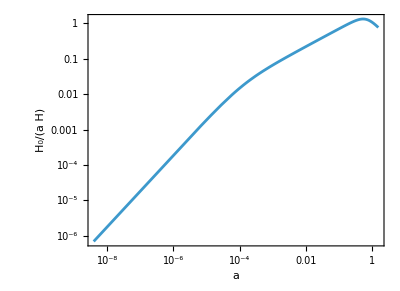

```mathematica
avHplot = ParametricPlot[{aasol[τ],aasol[τ]H00/(dasol[τ]*α)},{τ,τini,0.06},AxesLabel->{"a","H_0/(a H)"}, ScalingFunctions-> {"Log","Log"},PlotRange->All,Frame->True,AxesLabel->{"a","H_0/(a H)"}]
```